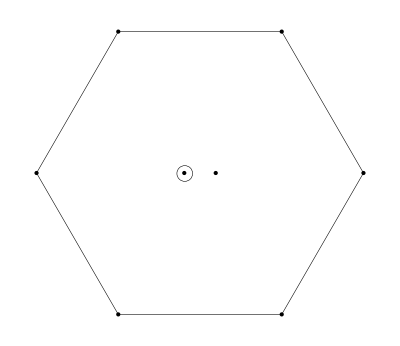

Y=0,  I_3=0

4uuūū-4sss̄s̄+(ud+du)(ūd̄+d̄ū)-(sd+ds)(s̄d̄+d̄s̄)

```mathematica
(*-------------------------------*)
```

The current J:

-((d_a^T C1 s_b+s_a^T C1 d_b) ((d̄)_a 1C((s̄)_b)^T))-(d_a^T C1 s_b+s_a^T C1 d_b) ((d̄)_b 1C((s̄)_a)^T)-(d_a^T C1 s_b+s_a^T C1 d_b) ((s̄)_a 1C((d̄)_b)^T)-(d_a^T C1 s_b+s_a^T C1 d_b) ((s̄)_b 1C((d̄)_a)^T)+(d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_a 1C((ū)_b)^T)+(d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_b 1C((ū)_a)^T)+(d_a^T C1 u_b+u_a^T C1 d_b) ((ū)_a 1C((d̄)_b)^T)+(d_a^T C1 u_b+u_a^T C1 d_b) ((ū)_b 1C((d̄)_a)^T)-4 (s_a^T C1 s_b) ((s̄)_a 1C((s̄)_b)^T+(s̄)_b 1C((s̄)_a)^T)+4 (u_a^T C1 u_b) ((ū)_a 1C((ū)_b)^T+(ū)_b 1C((ū)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 s-d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 d-d̄ γ^μ d s̄ γ^μ s-d̄ γ^μ s s̄ γ^μ d+d̄(γ̄)^5 s s̄(γ̄)^5 d-1/2 (d̄ σ^μν d s̄ σ^μν s)-1/2 (d̄ σ^μν s s̄ σ^μν d)+(d̄(γ̄)^5 d) (s̄(γ̄)^5 s-ū(γ̄)^5 u)+(d̄ 1d) (s̄ 1s-ū 1u)+d̄ 1s s̄ 1d+d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u+d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d+d̄ γ^μ d ū γ^μ u+d̄ γ^μ u ū γ^μ d-d̄(γ̄)^5 u ū(γ̄)^5 d+1/2 (d̄ σ^μν d ū σ^μν u)+1/2 (d̄ σ^μν u ū σ^μν d)-d̄ 1u ū 1d-2 (s̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 s)-2 (s̄ γ^μ s s̄ γ^μ s)+2 (s̄(γ̄)^5 s s̄(γ̄)^5 s)-s̄ σ^μν s s̄ σ^μν s+2 (s̄ 1s s̄ 1s)+2 (ū(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 u)+2 (ū γ^μ u ū γ^μ u)-2 (ū(γ̄)^5 u ū(γ̄)^5 u)+ū σ^μν u ū σ^μν u-2 (ū 1u ū 1u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(192 π^6)+(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(48 π^5)-(⟨ s̄ s⟩ log(-q^2/μ^2) (2 m_d+25 m_s) q^4)/(6 π^4)-(⟨ d̄ d⟩ log(-q^2/μ^2) (m_d+m_s+m_u) q^4)/(3 π^4)-(⟨ ū u⟩ log(-q^2/μ^2) (2 m_d+25 m_u) q^4)/(6 π^4)-(4 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(2 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(2 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(25 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(432 π^6)-(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(8 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(4 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(2 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)-(5 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2-(⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)-(⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(5 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(4 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(9 π q^2)-(14 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(3 π q^2)-(14 ⟨ GG ⟩ ⟨ ū u⟩^2)/(3 π q^2)-⟨ d̄ Gd⟩^2/(48 π^2 q^2)+(505 ⟨ s̄ Gs⟩^2)/(288 π^2 q^2)+(505 ⟨ ū Gu⟩^2)/(288 π^2 q^2)-(2 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)-(2 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)+(4 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)+(115 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(288 π^2 q^2)+(115 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(288 π^2 q^2)+(⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(48 π^2 q^2)+(32 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ m_d)/(3 q^2)+(4 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (8 m_d+4 m_s))/(9 q^2)-(4 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (88 m_s-4 m_d))/(9 q^2)+(4 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (8 m_d+4 m_u))/(9 q^2)-(4 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (88 m_u-4 m_d))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

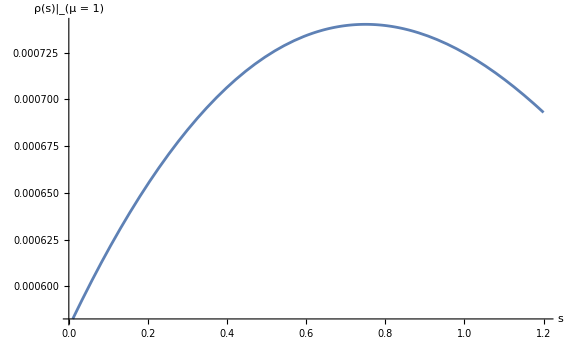
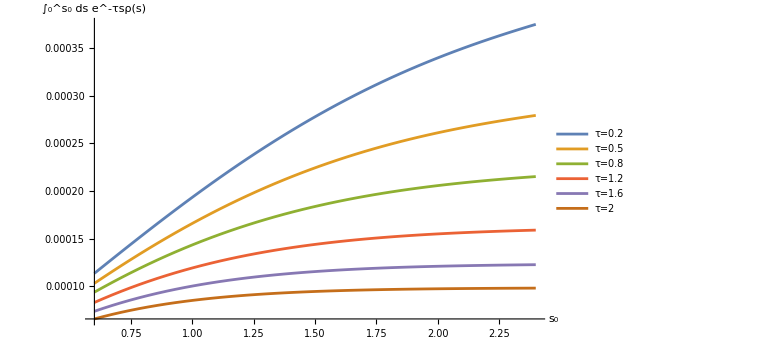

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

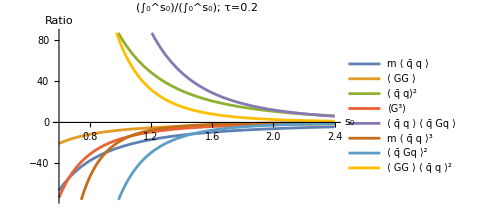
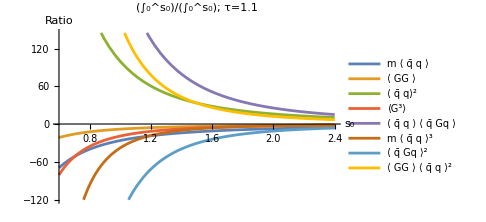
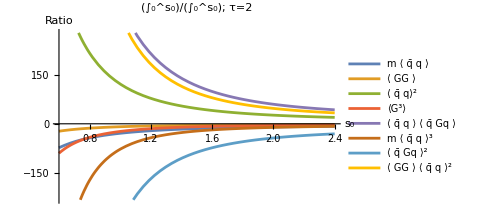

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

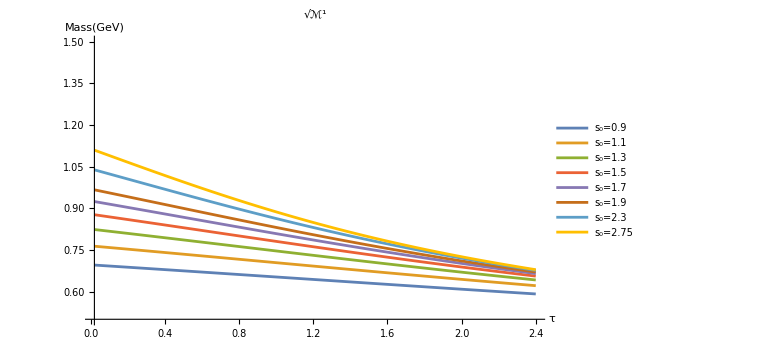
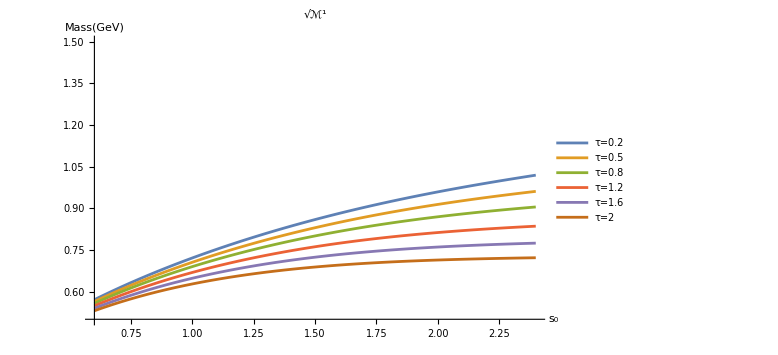

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

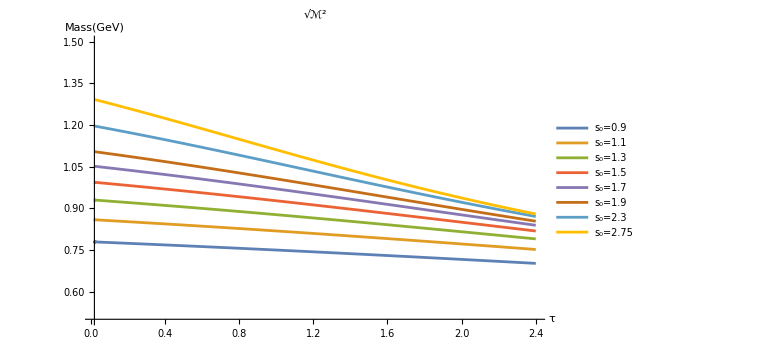
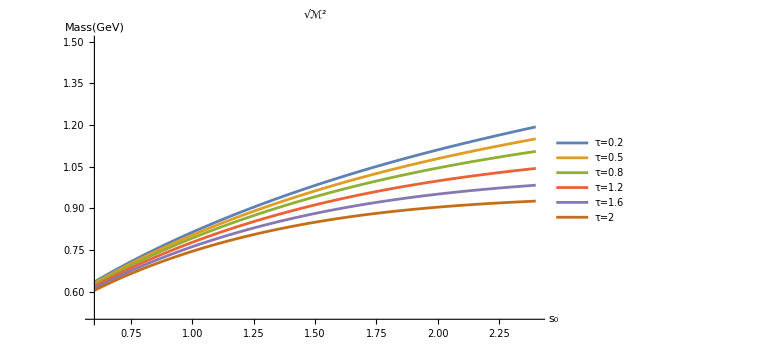

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

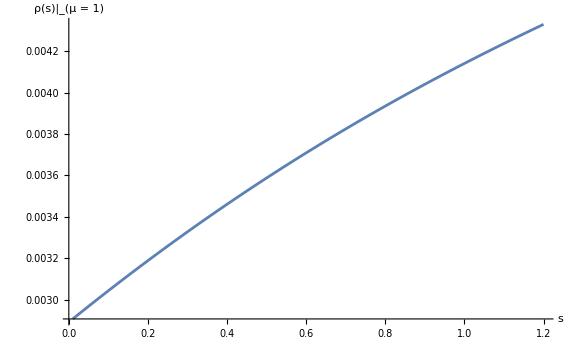
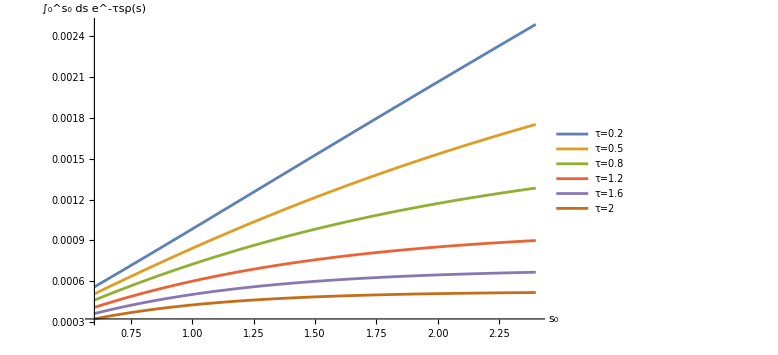

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

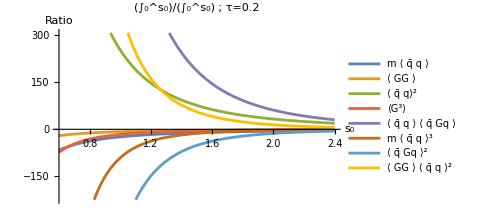
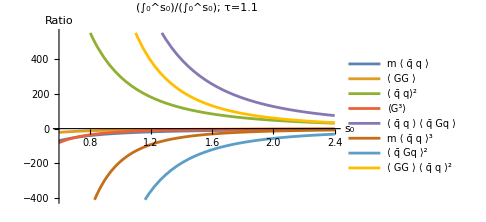
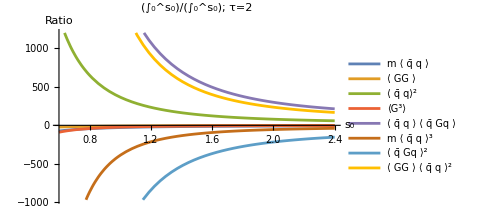

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

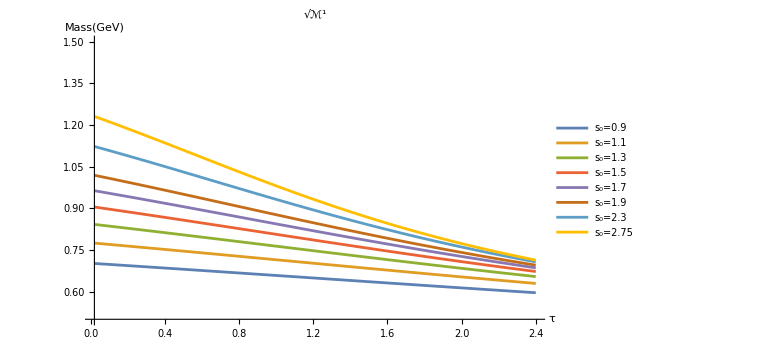
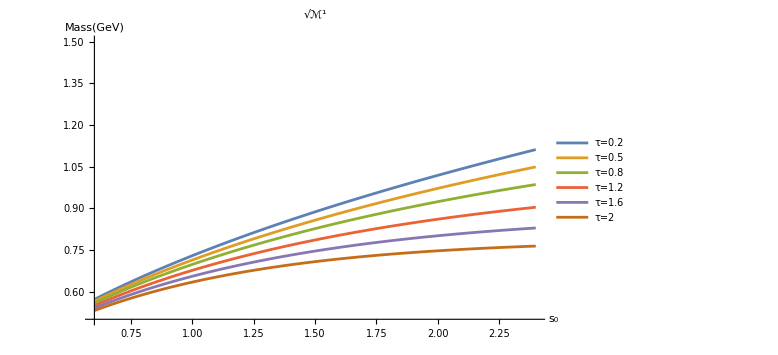

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5